# 3. Finite thin tube : calculations OFF axis

```mathematica
(* similar to thin tube on axis case, but different functions for getMagForce and flux derivative due to magnetic dipole *)
Clear["Global`*"];
```

```mathematica
(* physical parameters *)

a=0.05; (*radius of tube*)
h = 0.01;(*thickness of tube*)
(*h = a/3(1-(a/(a+h))^3);  (*effective thickness*) *)
H =0.5; (*length of tube*)
M = 0.0030; (* mass of the falling magnet*)
m = 2; (*dipole moment*)
σ=5.92 10^7; (*conductivity*)
μ =4π 10^-7; (*permeability*)
g = 0.2*9.81;
Y = 1/2; (* parameter giving distribution of current in ring body, Y=1/2 means uniform profile, more in  "Self inductance of a wire loop as a curve integral", R.Dengler, https://arxiv.org/pdf/1204.1486.pdf, I approximate the rectangular cross section of annular element of tube as circular cross section of a ring*)




(*simulation parameters*)

(* distance from cylindrical axis of symmetry *)
initHeight = 0.0 H; (* initial parallel coordinate of magnet: z[0] *)
initU = 0.2 a; (* initial radial coordinate of magnet: u[0] *)
tMax = 2.5;(*20*Sqrt[2(H+initHeight)/g]; in terms of time scale of free fall*)
n =100; (* number of partitions of the tube of length H *)
dζ = H/n; (* height of one ring, ζ is the general coordinate along tube axis from top opening, while z[t] denotes the position of magnet *) 
R = (2π a)/(σ h dζ); (*resistance of one elemental ring*)
indices=Range[n];  (* we will label the rings this way - their associated currents and their ζ coordinates will be derived from this *)
getζ[index_]:=-(index-1/2)  dζ  (* get coordinate of centre of ring measured from top end of tube *)
getζ[indices]; (* just for visual demonstration *)
J=ToExpression["J"<>ToString[#]]&/@indices; (* store all curents Subscript[J, index] in list J, NB: J is not current density but standard current in Amperes! *)


(* flux calculations - only take into account cutting flux from magnet, neglect self-induction at this stage *)

getFluxTDerFromTube[index_]:=0; (* approximation ! *)

(* the dominant contribution will be that of field from magnet directly, following calculates Subscript[dϕ, m]/dz, and dz/dt is provided in NDSolve as z'[t] *)

(* functions that calculate derivative of mag flux w.r.t. movement of magnet in z-direction, to be used in getFluxZDerFromMagnet *)
(* derivation of dependence in longMagdPhidz is given in separate file "derivations.nb" *)
longMagdPhidz[x_,y_]:=
(* this function calculates dϕ/dz based on reduced (i.e. /a ) relative (i.e. z-Subscript[z, ring]) position of magnet and given ring *)-μ/(4π)(3m)/a^2((x ((1+x^2-2 y+y^2)/(x^2+(-1+y)^2))^(3/2) (-2 (-7+x^4+6 y^2+y^4+2 x^2 (-3+y^2)) EllipticE[-(4 y)/(x^2+(-1+y)^2)]+2 (x^4+2 x^2 y (1+y)+(-1+y) (1+y)^3) EllipticK[-(4 y)/(x^2+(-1+y)^2)]))/(3 (1+x^2-2 y+y^2)^(3/2) (x^2+(1+y)^2)^2))

getFluxZDerFromMagnet[index_,z_,u_]:=Module[{x,y,defInt},
(* this function accepts absolute z, u coordinates and index of given ring, x and y are reduced relative coordinates z and u (NOT cartesian coords {x,y,z}!) *)
x = (z-getζ[index])/a;  
y=u/a;
(* definite integral in x,y giving the dϕ/dz for ring of "index", calculation is based on above function longMagdPhidz[x,y] *)
defInt = longMagdPhidz[x,y]
]
```

### Calculation of forces on falling magnet due to induced currents in the tube - first define off-axis expressions for radial and parallel componetns for ring and dipole, then sum them through all ring indices, the commented section hints at derivation of the long expressions

```mathematica
Print["Here are full equations for getRingFu and getRingFz - the expressions are too long and the cell can be hidden"]



getRingFu[index_,z_,u_,J_]:=-Module[{r,θ,ψ,Σ,Δζ},

Δζ=z-getζ[index];
{r,θ,ψ}=CoordinateTransformData["Cartesian"->"Spherical","Mapping",{u,0,Δζ}];
(*Σ=Sign[u];*) (* there are two allowed values of magnet's azimutal angle: 0 and 180 degrees -> u = +/-  *)
Σ=Cos[ψ];

1/(4 π r)J m μ Cos[θ] (-((2 Cot[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/((a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])^2))+(3 Cot[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/((a^2+r^2-2 a r Σ Sin[θ])^(5/2) (a^2+r^2+2 a r Σ Sin[θ]))-(Cot[θ] Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ]))+(Csc[θ] (-16 a^3 r^3 Σ^2 Cos[θ] EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ]^2-2 (a r (a^2+r^2) Cos[θ]-2 a^3 r Σ Cos[θ]) EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ])+4 a r Σ Cos[θ] EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r Cos[θ] EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)+1/(4 a r Σ)Csc[θ] (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]) (a^2+r^2-2 a r Σ Sin[θ])^2 (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ]) (-(8 a^2 r^2 Σ^2 Cos[θ] Sin[θ])/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a r Σ Cos[θ])/(a^2+r^2-2 a r Σ Sin[θ]))-1/(4 Σ (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))(a^2+r^2-2 a r Σ Sin[θ]) ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2) (-(8 a^2 r^2 Σ^2 Cos[θ] Sin[θ])/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a r Σ Cos[θ])/(a^2+r^2-2 a r Σ Sin[θ])) (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])))+1/(4 π)J m μ Sin[θ] (-((Csc[θ] (2 r+2 a Σ Sin[θ]) (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])^2))-(3 Csc[θ] (2 r-2 a Σ Sin[θ]) (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(2 a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(5/2) (a^2+r^2+2 a r Σ Sin[θ]))-(Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r^2 Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ]))+(Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (2 a r^2 Sin[θ]+a (a^2+r^2) Sin[θ]-2 a^3 Σ Sin[θ]) (a^2+r^2-2 a r Σ Sin[θ])-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (2 r-2 a Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] (4 r (a^2+r^2)-8 a^2 r Σ^2 Sin[θ]^2)+2 a EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)+1/(4 a r Σ)Csc[θ] (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]) (a^2+r^2-2 a r Σ Sin[θ])^2 (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ]) ((4 a r Σ Sin[θ] (2 r-2 a Σ Sin[θ]))/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ]))-1/(4 Σ (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))(a^2+r^2-2 a r Σ Sin[θ]) ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2) ((4 a r Σ Sin[θ] (2 r-2 a Σ Sin[θ]))/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])) (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])))]

getRingFz[index_,z_,u_,J_]:=-Module[{r,θ,ψ,Σ,Δζ},

(* "radius" and "theta" denote actual instantaneous values of coords r and θ of the falling magnet in frame of center of infinitesemal ring *)
Δζ=z-getζ[index];
{r,θ,ψ}=CoordinateTransformData["Cartesian"->"Spherical","Mapping",{u,0,Δζ}];
(*Σ=Sign[u];*) (* there are two allowed values of magnet's azimutal angle: 0 and 180 degrees -> u = +/-  *)
Σ=Cos[ψ];



+1/(4 π r)J m μ Sin[θ] (-((2 Cot[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/((a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])^2))+(3 Cot[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/((a^2+r^2-2 a r Σ Sin[θ])^(5/2) (a^2+r^2+2 a r Σ Sin[θ]))-(Cot[θ] Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ]))+(Csc[θ] (-16 a^3 r^3 Σ^2 Cos[θ] EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ]^2-2 (a r (a^2+r^2) Cos[θ]-2 a^3 r Σ Cos[θ]) EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ])+4 a r Σ Cos[θ] EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r Cos[θ] EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)+1/(4 a r Σ)Csc[θ] (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]) (a^2+r^2-2 a r Σ Sin[θ])^2 (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ]) (-(8 a^2 r^2 Σ^2 Cos[θ] Sin[θ])/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a r Σ Cos[θ])/(a^2+r^2-2 a r Σ Sin[θ]))-1/(4 Σ (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))(a^2+r^2-2 a r Σ Sin[θ]) ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2) (-(8 a^2 r^2 Σ^2 Cos[θ] Sin[θ])/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a r Σ Cos[θ])/(a^2+r^2-2 a r Σ Sin[θ])) (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])))-1/(4 π)J m μ Cos[θ] (-((Csc[θ] (2 r+2 a Σ Sin[θ]) (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])^2))-(3 Csc[θ] (2 r-2 a Σ Sin[θ]) (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(2 a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(5/2) (a^2+r^2+2 a r Σ Sin[θ]))-(Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (a^2+r^2-2 a r Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)))/(a r^2 Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ]))+(Csc[θ] (-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (2 a r^2 Sin[θ]+a (a^2+r^2) Sin[θ]-2 a^3 Σ Sin[θ]) (a^2+r^2-2 a r Σ Sin[θ])-2 EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (2 r-2 a Σ Sin[θ]) (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ])+2 a r EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] (4 r (a^2+r^2)-8 a^2 r Σ^2 Sin[θ]^2)+2 a EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] Sin[θ] ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2)+1/(4 a r Σ)Csc[θ] (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]) (a^2+r^2-2 a r Σ Sin[θ])^2 (a r (a^2+r^2) Sin[θ]-2 a^3 r Σ Sin[θ]) ((4 a r Σ Sin[θ] (2 r-2 a Σ Sin[θ]))/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ]))-1/(4 Σ (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))(a^2+r^2-2 a r Σ Sin[θ]) ((a^2+r^2)^2-4 a^2 r^2 Σ^2 Sin[θ]^2) ((4 a r Σ Sin[θ] (2 r-2 a Σ Sin[θ]))/((a^2+r^2-2 a r Σ Sin[θ])^2)-(4 a Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])) (EllipticE[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])]-EllipticK[-(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])] (1+(4 a r Σ Sin[θ])/(a^2+r^2-2 a r Σ Sin[θ])))))/(a r Σ (a^2+r^2-2 a r Σ Sin[θ])^(3/2) (a^2+r^2+2 a r Σ Sin[θ])))]
```

Here are full equations for getRingFu and getRingFz - the expressions are too long and the cell can be hidden

### Final calculations and solution with NDSolve

```mathematica
(* properly summed magnetic forces *)
(* now obtain the magnetic forces by summing partial contribution from all constitutive rings of the tube *)
getTotalMagForceZ[z_,u_,J_]:=Total[ getRingFz[#,z,u,J⟦#⟧[t]]&/@ indices]
getTotalMagForceU[z_,u_,J_]:=Total[ getRingFu[#,z,u,J⟦#⟧[t]]&/@ indices]

getTotalMagForceU[0,0.2 a,J]
```

-0.000159452 J1[t]+0.000042479 J10[t]+5.94736×10^-9 J100[t]+0.0000385927 J11[t]+0.0000339532 J12[t]+0.0000292601 J13[t]+0.0000248838 J14[t]+0.0000209886 J15[t]+0.0000176196 J16[t]+0.0000147577 J17[t]+0.0000123542 J18[t]+0.0000103498 J19[t]-0.000134564 J2[t]+8.68474×10^-6 J20[t]+7.30408×10^-6 J21[t]+6.15957×10^-6 J22[t]+5.21004×10^-6 J23[t]+4.42103×10^-6 J24[t]+3.76397×10^-6 J25[t]+3.21541×10^-6 J26[t]+2.75613×10^-6 J27[t]+2.37044×10^-6 J28[t]+2.04553×10^-6 J29[t]-0.0000936027 J3[t]+1.77094×10^-6 J30[t]+1.53813×10^-6 J31[t]+1.34011×10^-6 J32[t]+1.17114×10^-6 J33[t]+1.0265×10^-6 J34[t]+9.02302×10^-7 J35[t]+7.95337×10^-7 J36[t]+7.02938×10^-7 J37[t]+6.22889×10^-7 J38[t]+5.53345×10^-7 J39[t]-0.000048861 J4[t]+4.9276×10^-7 J40[t]+4.3984×10^-7 J41[t]+3.93495×10^-7 J42[t]+3.52806×10^-7 J43[t]+3.16995×10^-7 J44[t]+2.85403×10^-7 J45[t]+2.57469×10^-7 J46[t]+2.32715×10^-7 J47[t]+2.1073×10^-7 J48[t]+1.91164×10^-7 J49[t]-0.0000101661 J5[t]+1.73716×10^-7 J50[t]+1.58126×10^-7 J51[t]+1.44169×10^-7 J52[t]+1.31652×10^-7 J53[t]+1.20404×10^-7 J54[t]+1.10281×10^-7 J55[t]+1.01154×10^-7 J56[t]+9.29108×10^-8 J57[t]+8.5455×10^-8 J58[t]+7.87005×10^-8 J59[t]+0.0000177755 J6[t]+7.25722×10^-8 J60[t]+6.70037×10^-8 J61[t]+6.19368×10^-8 J62[t]+5.73199×10^-8 J63[t]+5.31073×10^-8 J64[t]+4.92586×10^-8 J65[t]+4.57379×10^-8 J66[t]+4.25131×10^-8 J67[t]+3.95559×10^-8 J68[t]+3.68408×10^-8 J69[t]+0.0000346767 J7[t]+3.43451×10^-8 J70[t]+3.20486×10^-8 J71[t]+2.9933×10^-8 J72[t]+2.7982×10^-8 J73[t]+2.61809×10^-8 J74[t]+2.45166×10^-8 J75[t]+2.2977×10^-8 J76[t]+2.15515×10^-8 J77[t]+2.02304×10^-8 J78[t]+1.90049×10^-8 J79[t]+0.0000426438 J8[t]+1.78671×10^-8 J80[t]+1.68097×10^-8 J81[t]+1.58262×10^-8 J82[t]+1.49108×10^-8 J83[t]+1.40579×10^-8 J84[t]+1.32627×10^-8 J85[t]+1.25207×10^-8 J86[t]+1.18278×10^-8 J87[t]+1.11802×10^-8 J88[t]+1.05746×10^-8 J89[t]+0.0000444306 J9[t]+1.00078×10^-8 J90[t]+9.47697×10^-9 J91[t]+8.97947×10^-9 J92[t]+8.51288×10^-9 J93[t]+8.07501×10^-9 J94[t]+7.66381×10^-9 J95[t]+7.27742×10^-9 J96[t]+6.9141×10^-9 J97[t]+6.57228×10^-9 J98[t]+6.25048×10^-9 J99[t]

```mathematica
getRingFz[indices, 0, 0.2a,J]
```

A+B+C+D

{2.14978×10^-20 J1,2.14978×10^-20 J2,2.14978×10^-20 J3,2.14978×10^-20 J4}

```mathematica
(* Solving the n+2 EoMs *)
EoMs = Flatten[{M z''[t]==-M g + getTotalMagForceZ[z[t],u[t],J],M u''[t]==getTotalMagForceU[z[t],u[t],J], 
(R J⟦#⟧[t] == (-z'[t]getFluxZDerFromMagnet[#,z[t],u[t]] - getFluxTDerFromTube[#])&/@ indices) }];
BCs= Flatten[{z[0]==initHeight,z'[0]==0, u[0]==initU,u'[0]==0,(#[0]==0)&/@J}];
Join[EoMs,BCs];
timeSol = Timing[NDSolve[Join[EoMs,BCs],Flatten[{z,u,J}],{t,0,tMax},Method->{"EquationSimplification"->"Residual"},MaxSteps->Infinity]];
Print["simulation took "<>ToString[timeSol⟦1⟧]<>" seconds"]
sol =timeSol⟦2⟧;
```

simulation took 60.575 seconds

-Graphics-

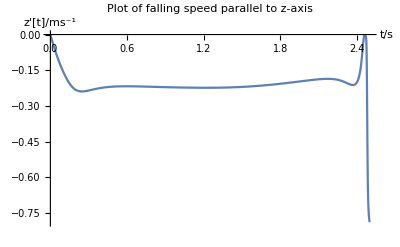

-Graphics-

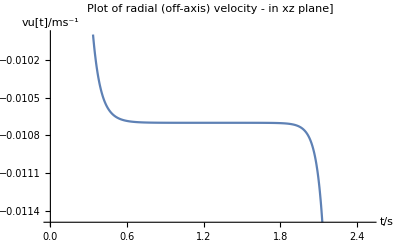

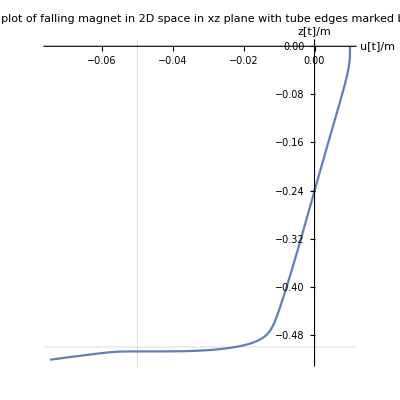

-Graphics-

Desktop/Internship_summer2020/research_notebooks/mathematica_arrays/sim1_Z.dat

Desktop/Internship_summer2020/research_notebooks/mathematica_arrays/sim1_U.dat

{{0.},{-9.81000000000000221×10^-7},{-3.92400110053414428×10^-6},{-8.81018359776241568×10^-6},{-0.000015630273618254208},2490,{-0.561462543583590712},{-0.561931197927297066},{-0.562401691911043056},{-0.562874028841238605},{-0.563348211942340638}}
 |  |  |  |

{{0.0100000000000000019},{0.0100000000000000019},{0.009999999999999963779},{0.0100000000925776263},{0.0100000003233551658},2490,{-0.0198497760749934207},{-0.0198917739300862526},{-0.0199338132567866283},{-0.0199758929720772263},{-0.0200180120162581007}}
 |  |  |  |

Plot::pllim: Range specification {{0.},{-9.81000000000000221×10^-7},{-3.92400110053414428×10^-6},{-8.81018359776241568×10^-6},{-0.000015630273618254208},{-0.0000243750189298979319},«40»,{-0.00193166391034508785},{-0.00201344995647579836},{-0.00209680209216547365},{-0.00218171281440945105},«2450»} is not of the form {x, xmin, xmax}.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[listUPy,listZPy]].

Show[-Graphics-,Plot[listUPy,listZPy]]

```mathematica
(* tMax = 0.3; *)

(* extract relevant interpolating functions "ifn's" *)
ifnZ = sol[[1,1,2]];
ifnU = sol[[1,2,2]];
ifnJ = sol[[1,#,2]]&/@Range[3,n+1,1];


Plot[{ifnZ[t](*,initHeight-1/2 g t^2*),Callout[-H,"end of tube"],Callout[0,"beginning of tube"]},{t,0,tMax},AxesLabel->{"t/s","z[t]/m"}, PlotLabel->"Plot of displacement parallel to z-axis"]
Plot[{ifnZ'[t](*,-g t*)},{t,0,tMax},AxesLabel->{"t/s","z'[t]/ms^-1"},PlotLabel->"Plot of falling speed parallel to z-axis",PlotRange->All]
Plot[{ifnU[t],Callout[-a,"left edge"],Callout[+a,"right edge"]},{t,0,tMax},PlotLabel->"Plot of radial (off-axis) displacement - in xz plane]",AxesLabel->{"t/s","u[t]/m"}]
Plot[{ifnU'[t]},{t,0,tMax},PlotLabel->"Plot of radial (off-axis) velocity - in xz plane]",AxesLabel->{"t/s","vu[t]/ms^-1"}]
ParametricPlot[{ifnU[t],ifnZ[t]},{t,0,tMax},GridLines->{{-a,+a},{0,-H}},PlotLabel->"Parametric plot of falling magnet in 2D space in xz plane with tube edges marked by gridlines",AxesLabel->{"u[t]/m","z[t]/m"},AspectRatio->1,PlotRange->{{-2a,2a},{0.1H,-1.5H}}]
Show[Plot[Callout[ifnJ⟦#⟧[t],"J"<>ToString[#],Bottom],{t,0,tMax}]&/@Range[1,n,n/5], PlotRange->All, PlotLabel->"Currents J_k[t] for selected k",AxesLabel->{"t/s","J_k[t]/A"}, PlotRange->All]

lengthOfList = 1000;
listT = Range[lengthOfList]/lengthOfList * tMax;
listZ = ifnZ[#]&/@listT;
listU = ifnU[#]&/@listT;

Export["Desktop/Internship_summer2020/research_notebooks/mathematica_arrays/sim1_Z.dat",listZ]
Export["Desktop/Internship_summer2020/research_notebooks/mathematica_arrays/sim1_U.dat",listU]

listZPy =Import["Desktop/Internship_summer2020/research_notebooks/python_arrays/3_z_N100_iter2500_t2.5"]
listUPy =Import["Desktop/Internship_summer2020/research_notebooks/python_arrays/3_x_N100_iter2500_t2.5"]

Show[ParametricPlot[{ifnU[t],ifnZ[t]},{t,0,tMax},GridLines->{{-a,+a},{0,-H}},PlotLabel->"Parametric plot of falling magnet in 2D space in xz plane with tube edges marked by gridlines",AxesLabel->{"u[t]/m","z[t]/m"},AspectRatio->1,PlotRange->{{-2a,2a},{0.1H,-1.5H}}], Plot[listUPy, listZPy]]
```

### Discarded/not used code relevant to this notebook

```mathematica
CoordinateTransformData["Cartesian"->"Spherical","Mapping",{-1,0,1}]
```

{√2,π/4,π}

```mathematica
(* calculation of mutual inductance of distant current loops *)
(* this is independent of on/off-axis position of magnet, just the values of currents will be different *)
(*formula for quick calculation of self inductane of ring of cross section "radius" h/2 and main radius a *)
(*selfInductanceRing = μ a (Log[(8a)/(h/2)]-2+Y/2) ;*)
(*Mutual Inductance and Inductance Calculations by Maxwell’s Method, from Antonio Carlos M.de Queiroz*)
(*calcMutInd[Δζ_]:=Module[{k},k=(2a)/(√(4 a^2+Δζ^2)); -a μ((k-2/k)EllipticK[k]+2/k EllipticE[k])]
(* calculate tube-induced flux derivative for a given index: sum contributions from all other elements (and finally-itself)*)
getFluxDerFromTube[index_]:=Total[  (calcMutInd[(index-#1)dζ]*J⟦#1⟧'[t])&/@   (Drop[indices,{index}])    ]       +      selfInductanceRing*J⟦index⟧'[t]
*)

(* dBzdz[ρ_,ϕ_,Δζ_,u_]:=-(3 m Δζ(-3 u^2+2 Δζ^2-3 ρ^2+6 u ρ Cos[ϕ]))/((u^2+Δζ^2+ρ^2-2 u ρ Cos[ϕ])^(7/2)) *)
```

### importing long expressions for off-axis forces and flux, NOT USED,they are included below (hidden cells)

```mathematica
(*
importAndRun[fileName_]:=Module[{nb},
nb=NotebookOpen[fileName];
	SelectionMove[nb,All,Notebook];
	SelectionEvaluate[nb];
	NotebookClose[nb];
]
importAndRun["/home/madm/Desktop/Internship_summer2020/research notebooks/longFz.nb"];
importAndRun["/home/madm/Desktop/Internship_summer2020/research notebooks/longFu.nb"];
importAndRun["/home/madm/Desktop/Internship_summer2020/research notebooks/longMagdPhidz.nb"];
*)
```

### Plotting graphs for forces and their spatial dependence

1

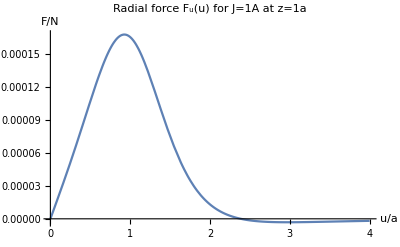

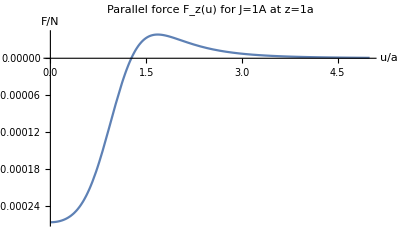

0.5

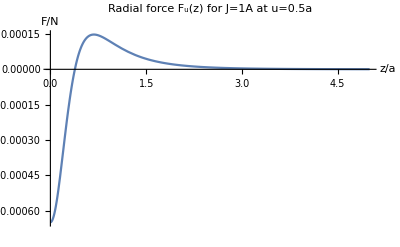

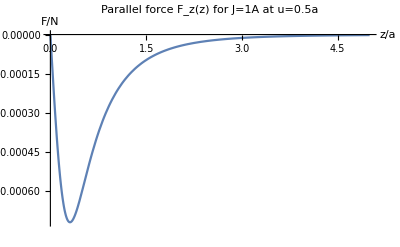

```mathematica
(*
fuValues=getRingFu[1/2,a,#,1]&/@Range[0,a,a/100];
fzValues=getRingFu[1/2,a,#,1]&/@Range[0,a,a/100];
*)

fix = 1;
Plot[getRingFu[1/2,fix*a,a*var,1],{var,0,4},PlotLabel-> "Radial force F_u(u) for J=1A at z="<>ToString[fix]<>"a",AxesLabel->{"u/a","F/N"} ]
Plot[getRingFz[1/2,fix*a,a*var,1],{var,0,5},PlotLabel-> "Parallel force F_z(u) for J=1A at z="<>ToString[fix]<>"a ",AxesLabel->{"u/a","F/N"},PlotRange->All ]

fix = 0.5;
Plot[getRingFu[1/2,var*a,fix*1a,1],{var,0,5},PlotLabel-> "Radial force F_u(z) for J=1A at u="<>ToString[fix]<>"a",AxesLabel->{"z/a","F/N"},PlotRange->All]
Plot[getRingFz[1/2,var*a,fix*a,1],{var,0,5},PlotLabel-> "Parallel force F_z(z) for J=1A at u="<>ToString[fix]<>"a",AxesLabel->{"z/a","F/N"},PlotRange->All ]
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```